```mathematica
Quit[];
```

## Central Limit

```mathematica
Gaussian[μ_,σ_]:=Exp[-(#-μ)^2/(2 σ^2)]/(Sqrt[2π] σ)&;
```

### n variables uniformly distributed

```mathematica
xclt[]:=RandomVariate[UniformDistribution[{-2,4}]];
```

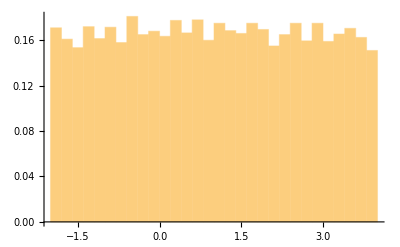

```mathematica
Histogram[Table[xclt[],{10^4}],Automatic,"PDF"]
```

```mathematica
Table[xclt[],{10^6}]//{Mean[#],Variance[#]}&
```

{0.997983,3.00218}

```mathematica
xsum=(Table[xclt[],{#}]/#//Total)&;
```

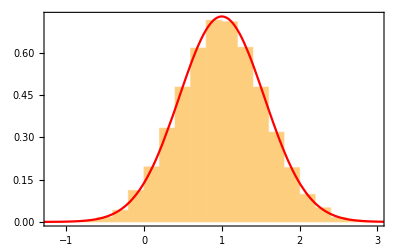

```mathematica
n=10;
Show[Histogram[Table[xsum[n],{10^4}],Automatic,"PDF"],Plot[Gaussian[1,Sqrt[3/n]][x],{x,-6,6},PlotRange->{All,{0,1.5}},PlotStyle->Red],Frame->True]
```

### n variables triangularly distributed

```mathematica
xclt[]:=RandomVariate[TriangularDistribution[{-2,4}]];
```

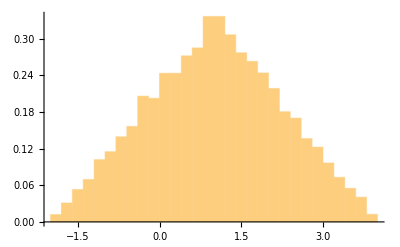

```mathematica
Histogram[Table[xclt[],{10^4}],Automatic,"PDF"]
```

```mathematica
Table[xclt[],{10^6}]//{Mean[#],Variance[#]}&
```

$Aborted

```mathematica
xsum=(Table[xclt[],{#}]/#//Total)&;
```

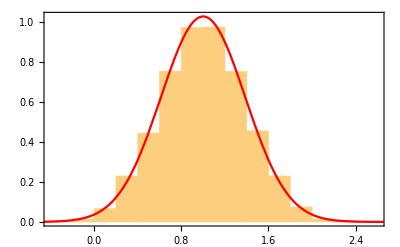

```mathematica
n=10;
Show[Histogram[Table[xsum[n],{10^4}],Automatic,"PDF"],Plot[Gaussian[1,Sqrt[1.5/n]][x],{x,-6,6},PlotRange->{All,{0,1.5}},PlotStyle->Red],Frame->True]
```

### n variables exponentially distributed

```mathematica
xclt[]:=RandomVariate[ExponentialDistribution[2]];
```

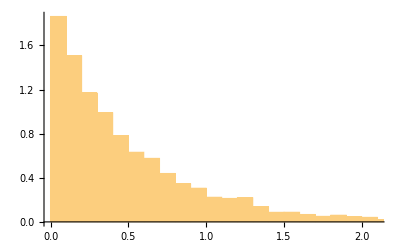

```mathematica
Histogram[Table[xclt[],{10^4}],Automatic,"PDF"]
```

```mathematica
Integrate[x λ Exp[-λ x],{x,0,Infinity},Assumptions->{λ>0}]
```

1/λ

```mathematica
Integrate[(x-1/λ)^2 λ Exp[-λ x],{x,0,Infinity},Assumptions->{λ>0}]
```

1/λ^2

```mathematica
Table[xclt[],{10^6}]//{Mean[#],Variance[#]}&
```

{0.499674,0.249464}

```mathematica
xsum=(Table[xclt[],{#}]/#//Total)&;
```

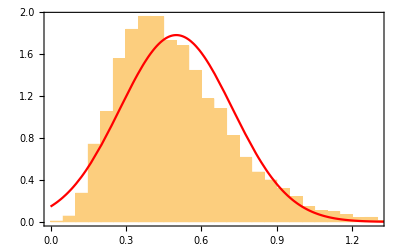

```mathematica
n=5;
Show[Histogram[Table[xsum[n],{10^4}],Automatic,"PDF"],Plot[Gaussian[1/2,Sqrt[1/4/n]][x],{x,0,2},PlotRange->{All,{0,8}},PlotStyle->Red],Frame->True]
```

## χ.b2 distribution

```mathematica
Gaussian[μ_,σ_]:=Exp[-(#-μ)^2/(2 σ^2)]/(Sqrt[2π] σ)&;
Chi2[n_]:=(#/2)^(n/2-1) Exp[-#/2]/2/Gamma[n/2]&;
```

### Plots χ.b2(n) distribution

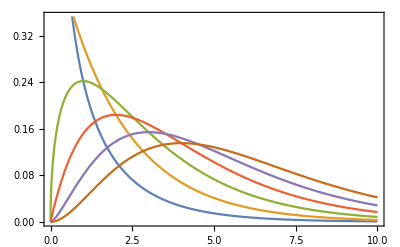

```mathematica
Plot[Table[Chi2[n][x],{n,1,6}]//Evaluate,{x,0,10},Frame->True]
```

```mathematica
Plot[Table[PDF[ChiSquareDistribution[n],x],{n,1,6}]//Evaluate,{x,0,10},Frame->True]
```

-Graphics-

### Distribution of sum of squares of gaussians

```mathematica
μi=RandomReal[{-5,5},10];
σi=RandomReal[{0,2},10];
xi=Table[RandomVariate[NormalDistribution[μi⟦i⟧,σi⟦i⟧],10^7],{i,1,10}];
```

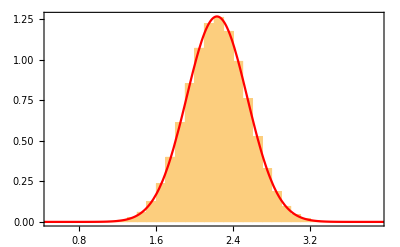

```mathematica
Show[Histogram[xi⟦1⟧,Automatic,"PDF"],Plot[Gaussian[μi⟦1⟧,σi⟦1⟧][x],{x,-6,6},PlotRange->{All,{0,1.5}},PlotStyle->Red],Frame->True]
```

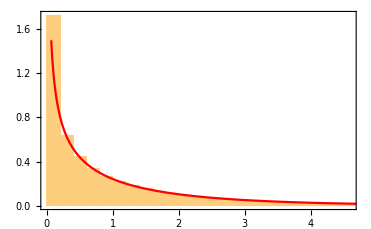

```mathematica
Show[Histogram[(xi⟦1⟧-μi⟦1⟧)^2/σi⟦1⟧^2,Automatic,"PDF"],Plot[Chi2[1][x],{x,0,20},PlotRange->{All,{0,1.5}},PlotStyle->Red],Frame->True]
```

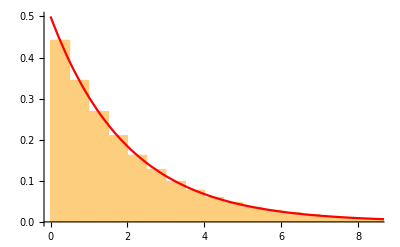

```mathematica
Show[Histogram[Sum[(xi⟦i⟧-μi⟦i⟧)^2/σi⟦i⟧^2,{i,1,2}],Automatic,"PDF"],Plot[Chi2[2][x],{x,0,20},PlotRange->{All,{0,0.5}},PlotStyle->Red]]
```

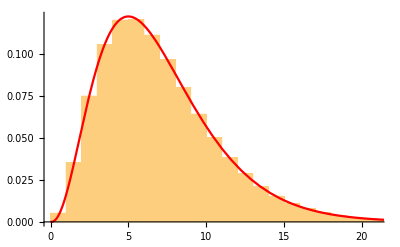

```mathematica
Show[Histogram[Sum[(xi⟦i⟧-μi⟦i⟧)^2/σi⟦i⟧^2,{i,1,7}],Automatic,"PDF"],Plot[Chi2[7][x],{x,0,30},PlotRange->{All,{0,0.35}},PlotStyle->Red]]
```

### Correlated case

```mathematica
ρ={{1,0.9},{0.9,1}};
cov=DiagonalMatrix[σi⟦1;;2⟧].ρ.DiagonalMatrix[σi⟦1;;2⟧];
xicorr=RandomVariate[MultinormalDistribution[μi⟦1;;2⟧,cov],10^5];
```

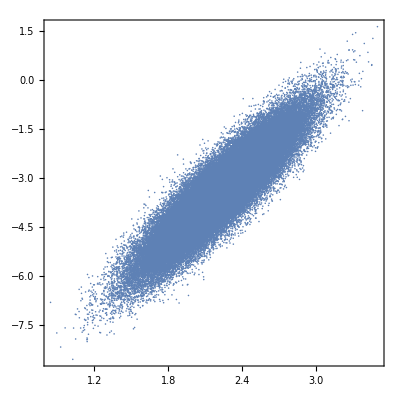

```mathematica
ListPlot[xicorr,AspectRatio->1,Frame->True]
```

```mathematica
ui=Table[(xicorr⟦i⟧-μi⟦1;;2⟧).Inverse[cov].(xicorr⟦i⟧-μi⟦1;;2⟧),{i,10^5}];
```

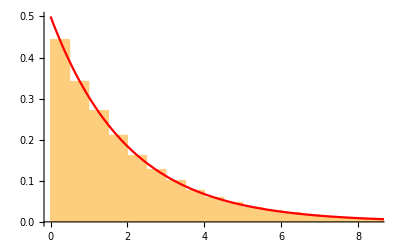

```mathematica
Show[Histogram[ui,Automatic,"PDF"],Plot[Chi2[2][x],{x,0,30},PlotRange->{All,{0,0.55}},PlotStyle->Red]]
```

## Capture/Recapture

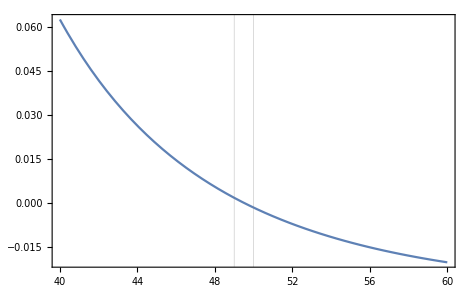

Solve::fexp: Warning: Solve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{{n→Root49.5Root[{PolyGamma[0,-25+#1]-PolyGamma[0,-19+#1]-PolyGamma[0,-9+#1]+PolyGamma[0,1+#1]&,49.4950014268950650347098764782119}]49.495001426895065}}

1.44329×10^-14

```mathematica
L=Binomial[n-10,16] Binomial[10,4]/Binomial[n,20];
Plot[D[Log[L],n]/.n->m,{m,40,60},Frame->True,GridLines->{{49,50},None}]
Solve[D[Log[L],n]==0,n,Assumptions->{n>25}]
(Log[L]/.n->50.)-(Log[L]/.n->49.)
```

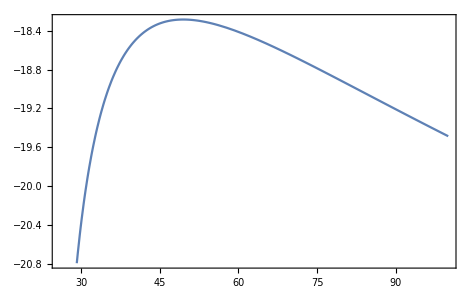

```mathematica
Plot[Sum[Log[n-k],{k,20,25}]-Sum[Log[n-k],{k,0,9}],{n,26,100},Frame->True]
```

## Hypothesis Tests: z-Test

### z-Test: H0 is true

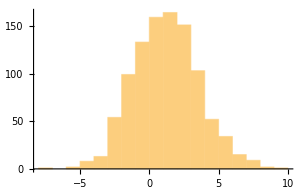

```mathematica
μ0=1.2;
Ndata=1000;
μdata=μ0;
σdata=2.3;
data=RandomVariate[NormalDistribution[μdata,σdata],{Ndata}];
Histogram[data]
```

```mathematica
(* This is what we would do *)
z=(Mean[data]-μ0)/(σdata/Sqrt[Ndata])
pvalue1=1-CDF[NormalDistribution[],z] (* Right-sided*)
pvalue2=CDF[NormalDistribution[],z] (* Left-sided*)
pvalue3=2CDF[NormalDistribution[],-Abs[z]] (* Two-sided*)
```

0.360679

0.35917

0.64083

0.718339

```mathematica
(* This is the Mathematica implementaion of the z-test *)
ZTest[data,σdata^2,μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
ZTest[data,σdata^2,μ0,"TestDataTable",AlternativeHypothesis->"Less"]
ZTest[data,σdata^2,μ0,"TestDataTable"]
```

| Statistic | P-Value
Z | 0.360679 | 0.35917

| Statistic | P-Value
Z | 0.360679 | 0.64083

| Statistic | P-Value
Z | 0.360679 | 0.718339

### z-Test: HA=H1 is true

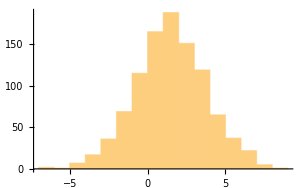

```mathematica
μ0=1.2;
Ndata=1000;
μdata=μ0+0.35;
σdata=2.3;
data=RandomVariate[NormalDistribution[μdata,σdata],{Ndata}];
Histogram[data]
```

```mathematica
ZTest[data,σdata^2,μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
ZTest[data,σdata^2,μ0,"TestDataTable",AlternativeHypothesis->"Less"]
ZTest[data,σdata^2,μ0,"TestDataTable"]
```

| Statistic | P-Value
Z | 3.75063 | 0.0000881952

| Statistic | P-Value
Z | 3.75063 | 0.999912

| Statistic | P-Value
Z | 3.75063 | 0.00017639

### z-Test: the data is not normally distributed

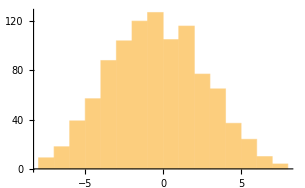

```mathematica
μ0=1.2;
Ndata=1000;
μdata=μ0+0.35;
σdata=2.3;
data=Join[RandomVariate[NormalDistribution[μdata,σdata],{Ndata/2}],RandomVariate[NormalDistribution[μdata-4,σdata],{Ndata/2}]];
Histogram[data]
```

```mathematica
ZTest[data,σdata^2,μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
ZTest[data,σdata^2,μ0,"TestDataTable",AlternativeHypothesis->"Less"]
ZTest[data,σdata^2,μ0,"TestDataTable"]
```

ZTest::nortst: At least one of the p-values in {0.0283455}, resulting from a test for normality, is below 0.05. The tests in {Z} require that the data is normally distributed.

| Statistic | P-Value
Z | -22.4381 | 1.

ZTest::nortst: At least one of the p-values in {0.0283455}, resulting from a test for normality, is below 0.05. The tests in {Z} require that the data is normally distributed.

| Statistic | P-Value
Z | -22.4381 | 8.36374×10^-112

ZTest::nortst: At least one of the p-values in {0.0283455}, resulting from a test for normality, is below 0.05. The tests in {Z} require that the data is normally distributed.

| Statistic | P-Value
Z | -22.4381 | 1.67275×10^-111

## Hypothesis Tests: one-sample t-Test

### t-statistic is Student's t

```mathematica
(* A function that generates a value for the t-statistic with ndof dofs*)
Generatet[ndof_]:=Module[{data,μ0,σ0},
μ0=Random[];σ0=Random[];data=RandomVariate[NormalDistribution[μ0,σ0],{ndof+1}];
(Mean[data]-μ0)/(StandardDeviation[data]/Sqrt[ndof+1])];
```

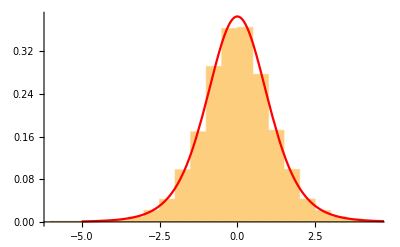

```mathematica
(* The variable t is distributed as a student's t with Ndof *)
Ndof=7;
ti=Table[Generatet[Ndof],{10^4}];
Show[Histogram[ti,Automatic,"PDF"],Plot[PDF[StudentTDistribution[Ndof],x],{x,-5,5},PlotRange->{All,{0,0.55}},PlotStyle->Red]]
```

### t-Test: H0 is true

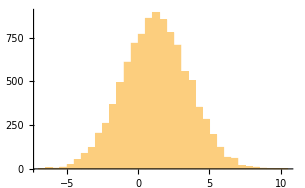

```mathematica
μ0=1.2;
Ndata=10000;
μdata=μ0;
σdata=2.3;
data=RandomVariate[NormalDistribution[μdata,σdata],{Ndata}];
Histogram[data]
```

```mathematica
(* This is what we would do *)
t=(Mean[data]-μ0)/(StandardDeviation[data]/Sqrt[Ndata])
pvalue1=1-CDF[StudentTDistribution[Ndata-1],t] (* Right-sided*)
pvalue2=CDF[StudentTDistribution[Ndata-1],t] (* Left-sided*)
pvalue3=2CDF[StudentTDistribution[Ndata-1],-Abs[t]] (* Two-sided*)
```

1.67755

0.0467332

0.953267

0.0934664

```mathematica
(* This is the Mathematica implementaion of the z-test *)
TTest[data,μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
TTest[data,μ0,"TestDataTable",AlternativeHypothesis->"Less"]
TTest[data,μ0,"TestDataTable"]
```

| Statistic | P-Value
T | 1.67755 | 0.0467332

| Statistic | P-Value
T | 1.67755 | 0.953267

| Statistic | P-Value
T | 1.67755 | 0.0934664

### t-Test: HA=H1 is true

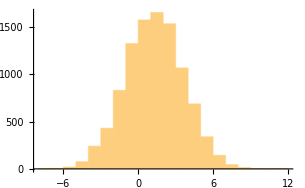

```mathematica
μ0=1.2;
Ndata=10000;
μdata=μ0+0.1;
σdata=2.3;
data=RandomVariate[NormalDistribution[μdata,σdata],{Ndata}];
Histogram[data]
```

```mathematica
(* This is the Mathematica implementaion of the z-test *)
TTest[data,μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
TTest[data,μ0,"TestDataTable",AlternativeHypothesis->"Less"]
TTest[data,μ0,"TestDataTable"]
```

| Statistic | P-Value
T | 4.14334 | 0.0000172555

| Statistic | P-Value
T | 4.14334 | 0.999983

| Statistic | P-Value
T | 4.14334 | 0.000034511

### t-Test: the data is not normally distributed

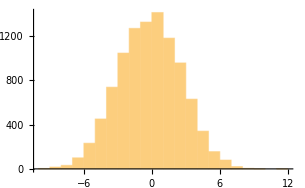

```mathematica
μ0=1.2;
Ndata=10000;
μdata=μ0+0.1;
σdata=2.3;
data=Join[RandomVariate[NormalDistribution[μdata,σdata],{Ndata/2}],RandomVariate[NormalDistribution[μdata-3,σdata],{Ndata/2}]];
Histogram[data]
```

```mathematica
(* This is the Mathematica implementaion of the z-test *)
TTest[data,μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
TTest[data,μ0,"TestDataTable",AlternativeHypothesis->"Less"]
TTest[data,μ0,"TestDataTable"]
```

TTest::nortst: At least one of the p-values in {0.000413775}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

| Statistic | P-Value
T | -50.961 | 1.

TTest::nortst: At least one of the p-values in {0.000413775}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

General::munfl: 4.0617664459073044841246×10^-504 is too small to represent as a normalized machine number; precision may be lost.

| Statistic | P-Value
T | -50.961 | 0.

TTest::nortst: At least one of the p-values in {0.000413775}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

General::munfl: 4.0617664459073044841246×10^-504 is too small to represent as a normalized machine number; precision may be lost.

| Statistic | P-Value
T | -50.961 | 0.

## Hypothesis Tests: two-sample t-Test

### two-sample t-statistic is Student's t

```mathematica
(* A function that generates a value for the t-statistic with ndof dofs*)
Generatet2[ndof_]:=Module[{ndata1,ndata2,data1,data2,μ1,μ2,σ,PooledVariance},
μ1=Random[]; μ2=Random[];
σ=RandomReal[{0,2}];
ndata1=RandomInteger[{2,ndof}];
ndata2=ndof-ndata1+2;
data1=RandomVariate[NormalDistribution[μ1,σ],{ndata1}];
data2=RandomVariate[NormalDistribution[μ2,σ],{ndata2}];
PooledVariance=(1/ndata1+1/ndata2)/ndof((ndata1-1)Variance[data1]+(ndata2-1)Variance[data2]);
(Mean[data1]-Mean[data2]-(μ1-μ2))/Sqrt[PooledVariance]];
```

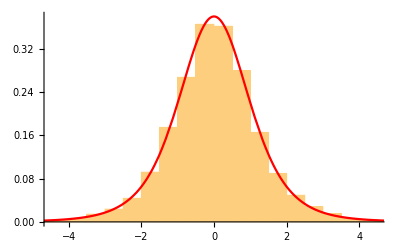

```mathematica
(* The variable t is distributed as a student's t with Ndof *)
Ndof=5;
ti=Table[Generatet2[Ndof],{10^4}];
Show[Histogram[ti,Automatic,"PDF"],Plot[PDF[StudentTDistribution[Ndof],x],{x,-5,5},PlotRange->{All,{0,0.55}},PlotStyle->Red]]
```

### two-sample t-Test: H0 is true

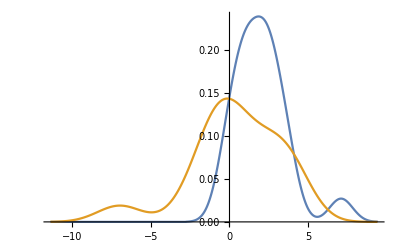

```mathematica
μ0=1.2;
Ndata1=20;
Ndata2=15;
μdata1=1.5;
μdata2=0.3;
σdata=2.3;
data1=RandomVariate[NormalDistribution[μdata1,σdata],{Ndata1}];
data2=RandomVariate[NormalDistribution[μdata2,σdata],{Ndata2}];
SmoothHistogram[{data1,data2}]
```

```mathematica
(* This is the Mathematica implementaion of the t-test *)
TTest[{data1,data2},μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
TTest[{data1,data2},μ0,"TestDataTable",AlternativeHypothesis->"Less"]
TTest[{data1,data2},μ0,"TestDataTable"]
```

| Statistic | P-Value
T | 0.504273 | 0.309621

| Statistic | P-Value
T | 0.504273 | 0.690379

| Statistic | P-Value
T | 0.504273 | 0.619243

### two-sample t-Test: HA=H1 is true

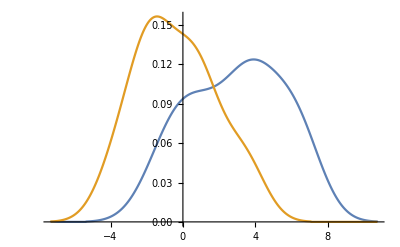

```mathematica
μ0=1.2;
Ndata1=20;
Ndata2=15;
μdata1=2.9;
μdata2=-0.7;
σdata=2.3;
data1=RandomVariate[NormalDistribution[μdata1,σdata],{Ndata1}];
data2=RandomVariate[NormalDistribution[μdata2,σdata],{Ndata2}];
SmoothHistogram[{data1,data2}]
```

```mathematica
(* This is the Mathematica implementaion of the t-test *)
TTest[{data1,data2},μ0,"TestDataTable",AlternativeHypothesis->"Greater"]
TTest[{data1,data2},μ0,"TestDataTable",AlternativeHypothesis->"Less"]
TTest[{data1,data2},μ0,"TestDataTable"]
```

| Statistic | P-Value
T | 2.54491 | 0.00789534

| Statistic | P-Value
T | 2.54491 | 0.992105

| Statistic | P-Value
T | 2.54491 | 0.0157907

## Hypothesis Tests: Kolmogorov-Smirnov

### One - sample

```mathematica
Ndata=200;
data=RandomVariate[StudentTDistribution[13],{Ndata}];
```

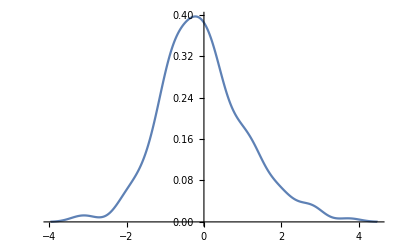

```mathematica
SmoothHistogram[data]
```

```mathematica
KolmogorovSmirnovTest[data,StudentTDistribution[13],"TestDataTable"]
KolmogorovSmirnovTest[data,StudentTDistribution[4],"TestDataTable"]
KolmogorovSmirnovTest[data,NormalDistribution[],"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.067956 | 0.30041

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0724085 | 0.233623

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0658866 | 0.335648

```mathematica
Ndata=2000;
data=RandomVariate[StudentTDistribution[13],{Ndata}];
```

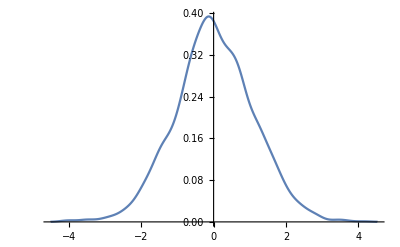

```mathematica
SmoothHistogram[data]
```

```mathematica
KolmogorovSmirnovTest[data,StudentTDistribution[13],"TestDataTable"]
KolmogorovSmirnovTest[data,StudentTDistribution[4],"TestDataTable"]
KolmogorovSmirnovTest[data,NormalDistribution[],"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0175413 | 0.563513

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0294135 | 0.0615822

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0279352 | 0.0865304

### Two - sample

```mathematica
Ndata1=400;
Ndata2=300;
Ndata3=600;
Ndata4=200;
data1=RandomVariate[StudentTDistribution[5],{Ndata1}];
data2=RandomVariate[StudentTDistribution[5],{Ndata2}];
data3=RandomVariate[NormalDistribution[],{Ndata3}];
data4=RandomVariate[TriangularDistribution[{-4,4}],{Ndata4}];
```

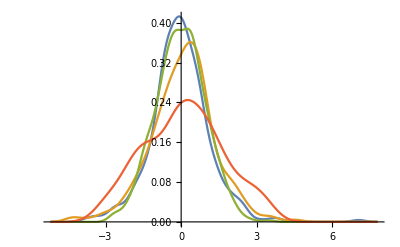

```mathematica
SmoothHistogram[{data1,data2,data3,data4}]
```

```mathematica
KolmogorovSmirnovTest[data1,data2,"TestDataTable"]
KolmogorovSmirnovTest[data1,data3,"TestDataTable"]
KolmogorovSmirnovTest[data2,data3,"TestDataTable"]
KolmogorovSmirnovTest[data1,data4,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.1075 | 0.0380444

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0425 | 0.778877

| Statistic | P-Value
Kolmogorov-Smirnov | 0.075 | 0.210552

| Statistic | P-Value
Kolmogorov-Smirnov | 0.165 | 0.00132728

```mathematica
Ndata1=4000;
Ndata2=3000;
Ndata3=6000;
Ndata4=2000;
data1=RandomVariate[StudentTDistribution[5],{Ndata1}];
data2=RandomVariate[StudentTDistribution[5],{Ndata2}];
data3=RandomVariate[NormalDistribution[],{Ndata3}];
data4=RandomVariate[TriangularDistribution[{-4,4}],{Ndata4}];
```

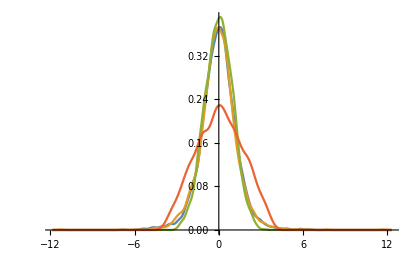

```mathematica
SmoothHistogram[{data1,data2,data3,data4}]
```

```mathematica
KolmogorovSmirnovTest[data1,data2,"TestDataTable"]
KolmogorovSmirnovTest[data1,data3,"TestDataTable"]
KolmogorovSmirnovTest[data2,data3,"TestDataTable"]
KolmogorovSmirnovTest[data1,data4,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.01725 | 0.687455

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0361667 | 0.0037523

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0428333 | 0.00129969

| Statistic | P-Value
Kolmogorov-Smirnov | 0.1265 | 0.

## Hypothesis Tests: ShapiroWilk vs KS

### One - sample H0 false

```mathematica
Ndata=200;
data=RandomVariate[StudentTDistribution[7],{Ndata}];
```

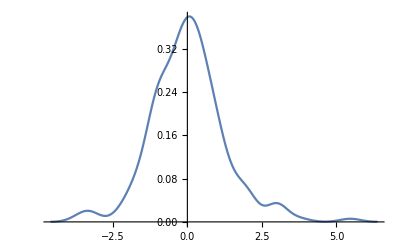

```mathematica
SmoothHistogram[data]
```

```mathematica
KolmogorovSmirnovTest[data,NormalDistribution[],"TestDataTable"]
ShapiroWilkTest[data,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0513125 | 0.648948

| Statistic | P-Value
Shapiro-Wilk | 0.965924 | 0.0000915426

```mathematica
Ndata=2000;
data=RandomVariate[StudentTDistribution[7],{Ndata}];
```

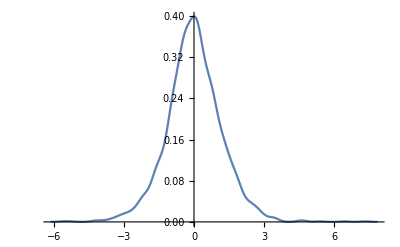

```mathematica
SmoothHistogram[data]
```

```mathematica
KolmogorovSmirnovTest[data,NormalDistribution[],"TestDataTable"]
ShapiroWilkTest[data,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0291319 | 0.0657923

| Statistic | P-Value
Shapiro-Wilk | 0.982504 | 6.09403×10^-15

### One - sample H0 true

```mathematica
Ndata=200;
data=RandomVariate[NormalDistribution[],{Ndata}];
```

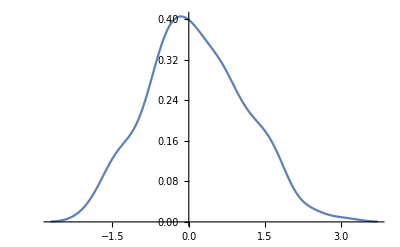

```mathematica
SmoothHistogram[data]
```

```mathematica
KolmogorovSmirnovTest[data,NormalDistribution[],"TestDataTable"]
ShapiroWilkTest[data,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0754465 | 0.194888

| Statistic | P-Value
Shapiro-Wilk | 0.992011 | 0.343199

```mathematica
Ndata=2000;
data=RandomVariate[NormalDistribution[],{Ndata}];
```

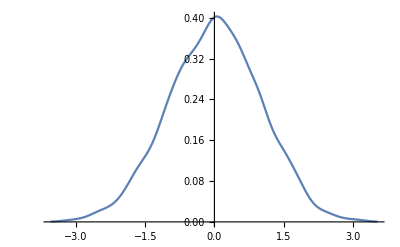

```mathematica
SmoothHistogram[data]
```

```mathematica
KolmogorovSmirnovTest[data,NormalDistribution[],"TestDataTable"]
ShapiroWilkTest[data,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0167374 | 0.62345

| Statistic | P-Value
Shapiro-Wilk | 0.999406 | 0.813273